```mathematica
f = Product[Cos[t/3^k], {k, 0, Infinity}]
```

∏_(k=0)^∞ Cos[3^-k t]

```mathematica
f = Power[E, I*t/2]* Product[Cos[t/3^k], {k, 0, 10}]
```

ⅇ^((ⅈ t)/2) Cos[t/59049] Cos[t/19683] Cos[t/6561] Cos[t/2187] Cos[t/729] Cos[t/243] Cos[t/81] Cos[t/27] Cos[t/9] Cos[t/3] Cos[t]

```mathematica
Plot[f, {t, -5, 5}]
```

-Graphics-

```mathematica
ComplexPlot3D[f, {t, -2-2I, 2+2I}]
```

-Graphics3D-

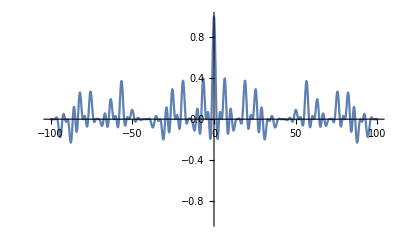

```mathematica
Plot[Re[f], {t, -100, 100}, PlotRange->{{-100, 100}, {-1, 1}}]
```

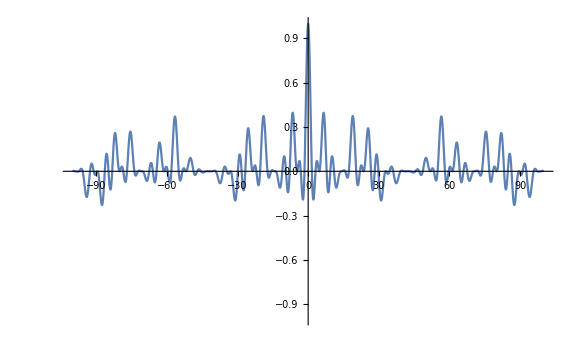

```mathematica
Show[%3,ImageSize->Large]
```

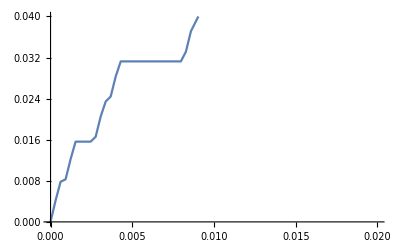

```mathematica
Plot[CantorStaircase[x],{x,0,1}, PlotRange->{{0, 0.02}, {0, 0.04}}]
```

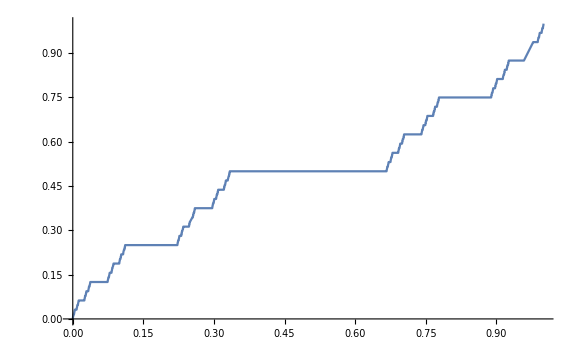

```mathematica
Show[%29,ImageSize->Large]
```

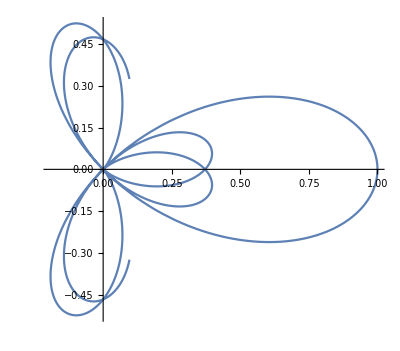

```mathematica
ParametricPlot[ReIm[f], {t, -10, 10}]
```

```mathematica
Plot[Re[f], {t, -100, 100}, PlotRange->{{-100, 100}, {-1, 1}}]
```

-Graphics-

```mathematica
g = Sum[(1/5)^n*Cos[13^n*Pi*x],{n,0,10}]
```

Cos[π x]+1/5 Cos[13 π x]+1/25 Cos[169 π x]+1/125 Cos[2197 π x]+1/625 Cos[28561 π x]+Cos[371293 π x]/3125+Cos[4826809 π x]/15625+Cos[62748517 π x]/78125+Cos[815730721 π x]/390625+Cos[10604499373 π x]/1953125+Cos[137858491849 π x]/9765625

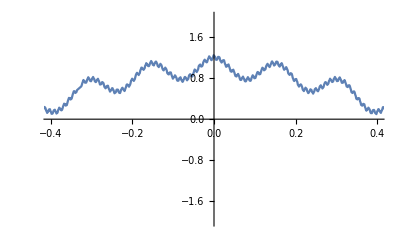

```mathematica
Plot[g, {x, -2,2}, PlotRange->{{-0.4, 0.4}, {-2, 2}}]
```

```mathematica
Integrate[g, x]
```

Sin[π x]/π+Sin[7 π x]/(21 π)+Sin[49 π x]/(441 π)+Sin[343 π x]/(9261 π)+Sin[2401 π x]/(194481 π)+Sin[16807 π x]/(4084101 π)+Sin[117649 π x]/(85766121 π)+Sin[823543 π x]/(1801088541 π)+Sin[5764801 π x]/(37822859361 π)+Sin[40353607 π x]/(794280046581 π)+Sin[282475249 π x]/(16679880978201 π)

```mathematica
Integrate[g, {x, -Pi/10, Pi/10}]
```

1/(1346274334462890625 π)2 (1346274334462890625 Sin[π^2/10]+20711912837890625 Sin[(13 π^2)/10]+318644812890625 Sin[(169 π^2)/10]+4902227890625 Sin[(2197 π^2)/10]+75418890625 Sin[(28561 π^2)/10]+1160290625 Sin[(371293 π^2)/10]+17850625 Sin[(4826809 π^2)/10]+274625 Sin[(62748517 π^2)/10]+4225 Sin[(815730721 π^2)/10]+65 Sin[(10604499373 π^2)/10]+Sin[(137858491849 π^2)/10])

1/(1346274334462890625 π)2 (1346274334462890625 Sin[π^2]+20711912837890625 Sin[13 π^2]+318644812890625 Sin[169 π^2]+4902227890625 Sin[2197 π^2]+75418890625 Sin[28561 π^2]+1160290625 Sin[371293 π^2]+17850625 Sin[4826809 π^2]+274625 Sin[62748517 π^2]+4225 Sin[815730721 π^2]+65 Sin[10604499373 π^2]+Sin[137858491849 π^2])

```mathematica
h = Power[E, t*I-0.5*Power[t, 2]]
```

ⅇ^(ⅈ t-0.5 t^2)

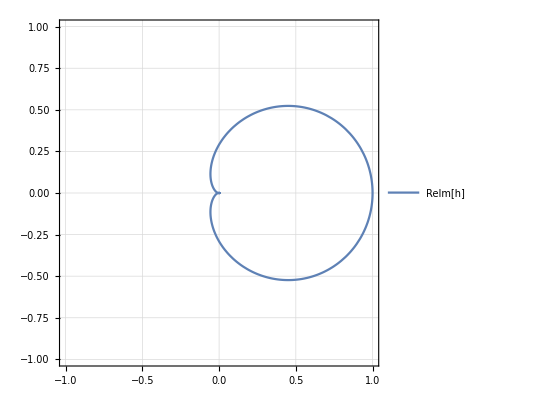

```mathematica
ParametricPlot[ReIm[h],{t,-14.696938456699069,14.696938456699069},PlotTheme->"Detailed",PlotRange->{{-1,1},{-1,1}}]
```

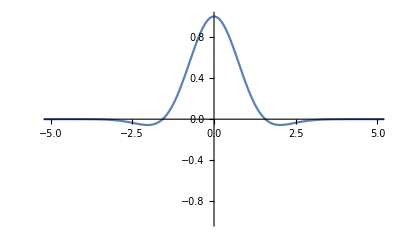

```mathematica
Plot[Re[h],{t,-14.696938456699069,14.696938456699069}, PlotRange->{{-5, 5}, {-1, 1}}]
```

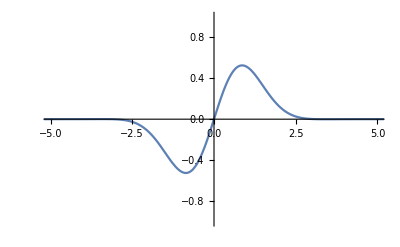

```mathematica
Plot[Im[h],{t,-14.696938456699069,14.696938456699069}, PlotRange->{{-5, 5}, {-1, 1}}]
```